```mathematica
({{2.1724007034307707 10^-06, 7.627221665219164 10^-12}, {2.7557343862331254 10^-07, 2.447248050160144 10^-11}, {8.205618931236921 10^-08, 8.717873270425288 10^-11}, {3.470344185902262 10^-08, 2.6548595026072 10^-10}, {1.779467642810426 10^-08, 7.518191694262277 10^-10}})
```

{{2.1724×10^-6,7.62722×10^-12},{2.75573×10^-7,2.44725×10^-11},{8.20562×10^-8,8.71787×10^-11},{3.47034×10^-8,2.65486×10^-10},{1.77947×10^-8,7.51819×10^-10}}

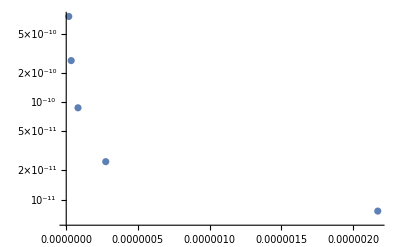

```mathematica
ListLogPlot[({{2.1724007034307707 10^-06, 7.627221665219164 10^-12}, {2.7557343862331254 10^-07, 2.447248050160144 10^-11}, {8.205618931236921 10^-08, 8.717873270425288 10^-11}, {3.470344185902262 10^-08, 2.6548595026072 10^-10}, {1.779467642810426 10^-08, 7.518191694262277 10^-10}})]
```

```mathematica
Fit[({{1/10, 7.627221665219164 10^-12}, {1/20, 2.447248050160144 10^-11}, {1/30, 8.717873270425288 10^-11}, {1/40, 2.6548595026072 10^-10}, {1/50, 7.518191694262277 10^-10}}), {1,x*x,x*x*x,x*x*x*x,x*x*x*x*x},x]
```

3.84996×10^-9-0.000021514 x^2+0.000954155 x^3-0.0147506 x^4+0.0732203 x^5

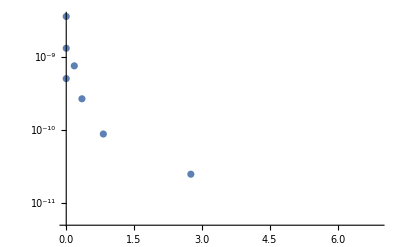

```mathematica
Show[ListLogPlot[({{2.1724007034307707 10^-06, 7.627221665219164 10^-12}, {2.7557343862331254 10^-07, 2.447248050160144 10^-11}, {8.205618931236921 10^-08, 8.717873270425288 10^-11}, {3.470344185902262 10^-08, 2.6548595026072 10^-10}, {1.779467642810426 10^-08, 7.518191694262277 10^-10}, {0, 5.022369353332074*^-10}, {0, 1.3124650421230262*^-9}, {0, 3.5832104696077976*^-9}})]]
```

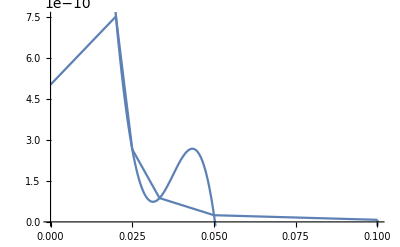

```mathematica
Show[ListPlot[({{1/10, 7.627221665219164 10^-12}, {1/20, 2.447248050160144 10^-11}, {1/30, 8.717873270425288 10^-11}, {1/40, 2.6548595026072 10^-10}, {1/50, 7.518191694262277 10^-10}, {0, 5.022369353332074*^-10}}),Joined->True],Plot[3.849961650525702*^-9-0.000021513983264548503 x^2+0.000954155357583962 x^3-0.014750605632454004 x^4+0.07322027038780633 x^5,{x,0,1/10}]]
```

```mathematica
Fit[({{10, 7.627221665219164 10^-12}, {20, 2.447248050160144 10^-11}, {30, 8.717873270425288 10^-11}, {40, 2.6548595026072 10^-10}, {50, 7.518191694262277 10^-10}}), {1,x*x,x*x*x,x*x*x*x,x*x*x*x*x},x]
```

1.08945×10^-11-1.54441×10^-13 x^2+1.62458×10^-14 x^3-4.72481×10^-16 x^4+6.55779×10^-18 x^5

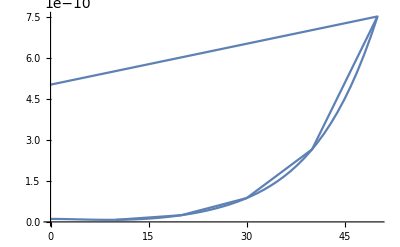

```mathematica
Show[ListPlot[({{10, 7.627221665219164 10^-12}, {20, 2.447248050160144 10^-11}, {30, 8.717873270425288 10^-11}, {40, 2.6548595026072 10^-10}, {50, 7.518191694262277 10^-10}, {0, 5.022369353332074*^-10}}),Joined->True],Plot[1.0894544916033504*^-11-1.5444075754222255*^-13 x^2+1.6245783574161538*^-14 x^3-4.724810267080642*^-16 x^4+6.557791963267067*^-18 x^5,{x,0,50}]]
```

PERFECT CONVERGENCE OF N → ∞ at gK = 0.5

Arrow

2.7127×10^-8-1.0486×10^-7 x

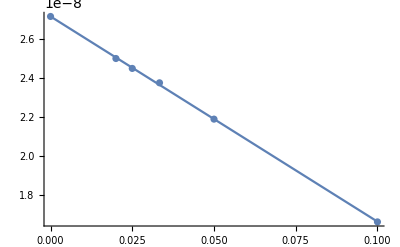

```mathematica
Fit[({{1/10, 1.6627452406022648 10^-08}, {1/20, 2.187969554094676 10^-08}, {1/30, 2.3735838401010163 10^-08}, {1/40, 2.4471009939116838 10^-08}, {1/50, 2.4978062835672475 10^-08}, {0, 2.7127005559869763 10^-08}}), {1,x},x]
Show[ListPlot[({{1/10, 1.6627452406022648 10^-08}, {1/20, 2.187969554094676 10^-08}, {1/30, 2.3735838401010163 10^-08}, {1/40, 2.4471009939116838 10^-08}, {1/50, 2.4978062835672475 10^-08}, {0, 2.7127005559869763 10^-08}}),Joined->False],Plot[2.7127005559869773*^-8-1.0485971683173706*^-7 x,{x,0,1/10}]]
```

PERFECT CONVERGENCE OF N → ∞ at gK = 0.6

3.95448×10^-7-1.1922×10^-6 x

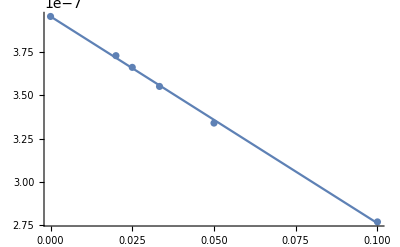

```mathematica
Fit[({{1/10, 2.7699946108616576 10^-07}, {1/20, 3.339749074065196 10^-07}, {1/30, 3.5510216633886407 10^-07}, {1/40, 3.660991149037772 10^-07}, {1/50, 3.7284619836748787 10^-07}, {0, 3.954481139219577 10^-07}}), {1,x},x]
Show[ListPlot[({{1/10, 2.7699946108616576 10^-07}, {1/20, 3.339749074065196 10^-07}, {1/30, 3.5510216633886407 10^-07}, {1/40, 3.660991149037772 10^-07}, {1/50, 3.7284619836748787 10^-07}, {0, 3.954481139219577 10^-07}}),Joined->False],Plot[3.9544811392195777*^-7-1.1921987803225125*^-6 x,{x,0,1/10}]]
```

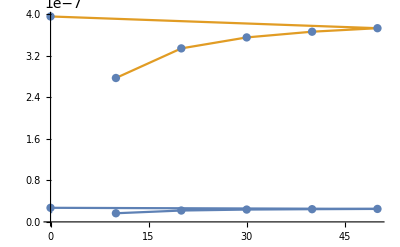

```mathematica
Show[ListPlot[{({{10, 1.6627452406022648 10^-08}, {20, 2.187969554094676 10^-08}, {30, 2.3735838401010163 10^-08}, {40, 2.4471009939116838 10^-08}, {50, 2.4978062835672475 10^-08}, {0, 2.7127005559869763 10^-08}}),({{10, 2.7699946108616576 10^-07}, {20, 3.339749074065196 10^-07}, {30, 3.5510216633886407 10^-07}, {40, 3.660991149037772 10^-07}, {50, 3.7284619836748787 10^-07}, {0, 3.954481139219577 10^-07}})},Joined->True,Mesh->Full],Plot[2.7127005559869773*^-8-1.0485971683173706*^-7 x,{x,0,1/10}]]
```

## sdsds

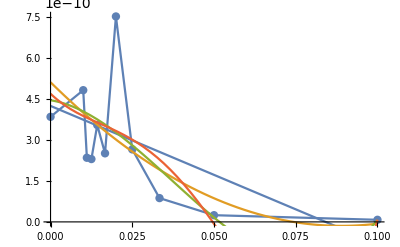

```mathematica
Show[ListPlot[({{1/10, 7.674666077912856 10^-12}, {1/20, 2.4535815109079297 10^-11}, {1/30, 8.708444839209839 10^-11}, {1/40, 2.653663285612071 10^-10}, {1/50, 7.518187679367473 10^-10}, {1/60, 2.5090720583733583 10^-10}, {1/70, 3.545487148344903 10^-10}, {1/80, 2.2998585117768087 10^-10}, {1/90, 2.34719649200822663 10^-10}, {1/100, 4.820264818576689 10^-10}, {0, 3.845355050645565*^-10}}),Joined->True,Mesh->Full],Plot[{4.24438504300376*^-10-5.0458678785048575*^-9 x,5.110541704348913*^-10-1.180874919686818*^-8 x+6.633601413488002*^-8 x^2,4.4515217134648114*^-10-1.873523573755296*^-9 x-2.4319397678895785*^-7 x^2+2.181087348169192*^-6 x^3,4.691374401202006*^-10-1.1501218774934947*^-8 x+4.538130690781062*^-7 x^2-0.000012722606210753499 x^3+0.00008873769159903554 x^4},{x,0,1/10}]]
```

```mathematica
Fit[({{1/10, 7.674666077912856 10^-12}, {1/20, 2.4535815109079297 10^-11}, {1/30, 8.708444839209839 10^-11}, {1/40, 2.653663285612071 10^-10}, {1/50, 7.518187679367473 10^-10}, {1/60, 2.5090720583733583 10^-10}, {1/70, 3.545487148344903 10^-10}, {1/80, 2.2998585117768087 10^-10}, {1/90, 2.34719649200822663 10^-10}, {1/100, 4.820264818576689 10^-10}, {0, 5.022369353332074*^-10}}), {1,x},x]
Fit[({{1/10, 7.674666077912856 10^-12}, {1/20, 2.4535815109079297 10^-11}, {1/30, 8.708444839209839 10^-11}, {1/40, 2.653663285612071 10^-10}, {1/50, 7.518187679367473 10^-10}, {1/60, 2.5090720583733583 10^-10}, {1/70, 3.545487148344903 10^-10}, {1/80, 2.2998585117768087 10^-10}, {1/90, 2.34719649200822663 10^-10}, {1/100, 4.820264818576689 10^-10}, {0, 5.022369353332074*^-10}}), {1,x,x*x},x]
Fit[({{1/10, 7.674666077912856 10^-12}, {1/20, 2.4535815109079297 10^-11}, {1/30, 8.708444839209839 10^-11}, {1/40, 2.653663285612071 10^-10}, {1/50, 7.518187679367473 10^-10}, {1/60, 2.5090720583733583 10^-10}, {1/70, 3.545487148344903 10^-10}, {1/80, 2.2998585117768087 10^-10}, {1/90, 2.34719649200822663 10^-10}, {1/100, 4.820264818576689 10^-10}, {0, 5.022369353332074*^-10}}), {1,x,x*x,x*x*x},x]
Fit[({{1/10, 7.674666077912856 10^-12}, {1/20, 2.4535815109079297 10^-11}, {1/30, 8.708444839209839 10^-11}, {1/40, 2.653663285612071 10^-10}, {1/50, 7.518187679367473 10^-10}, {1/60, 2.5090720583733583 10^-10}, {1/70, 3.545487148344903 10^-10}, {1/80, 2.2998585117768087 10^-10}, {1/90, 2.34719649200822663 10^-10}, {1/100, 4.820264818576689 10^-10}, {0, 5.022369353332074*^-10}}), {1,x,x*x,x*x*x,x*x*x*x},x]
```

4.24439×10^-10-5.04587×10^-9 x

5.11054×10^-10-1.18087×10^-8 x+6.6336×10^-8 x^2

4.45152×10^-10-1.87352×10^-9 x-2.43194×10^-7 x^2+2.18109×10^-6 x^3

4.69137×10^-10-1.15012×10^-8 x+4.53813×10^-7 x^2-0.0000127226 x^3+0.0000887377 x^4

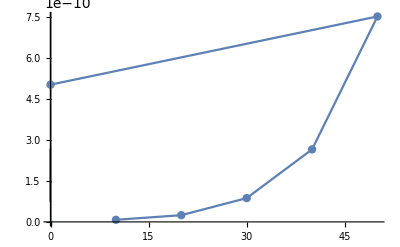

```mathematica
Show[ListPlot[({{10, 7.674666077912856 10^-12}, {20, 2.4535815109079297 10^-11}, {30, 8.708444839209839 10^-11}, {40, 2.653663285612071 10^-10}, {50, 7.518187679367473 10^-10}, {0, 5.022369353332074*^-10}}),Joined->True,Mesh->Full],Plot[3.849961650525702*^-9-0.000021513983264548503 x^2+0.000954155357583962 x^3-0.014750605632454004 x^4+0.07322027038780633 x^5,{x,0,1/10}]]
```

4.39015×10^-8-1.76547×10^-7 x

4.45107×10^-8-2.17513×10^-7 x+3.81168×10^-7 x^2

4.45561×10^-8-2.22383×10^-7 x+5.07658×10^-7 x^2-8.25452×10^-7 x^3

4.45794×10^-8-2.25951×10^-7 x+6.77178×10^-7 x^2-3.7794×10^-6 x^3+0.0000159238 x^4

4.43371×10^-8-1.76026×10^-7 x-2.94869×10^-6 x^2+0.000111471 x^3-0.00157751 x^4+0.00756015 x^5

4.46198×10^-8-2.50756×10^-7 x+4.58314×10^-6 x^2-0.000256536 x^3+0.00755013 x^4-0.100256 x^5+0.465281 x^6

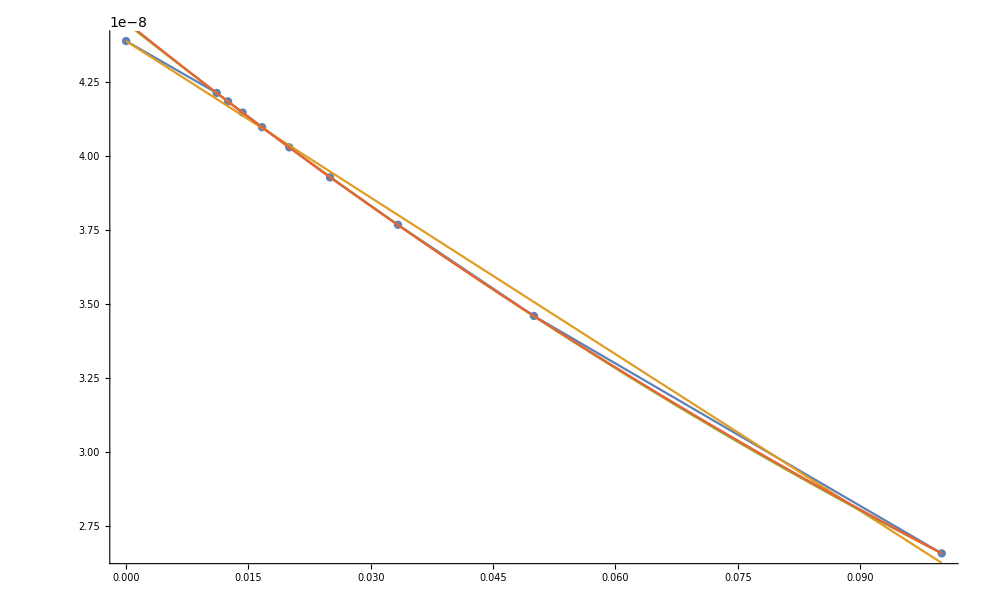

```mathematica
Fit[({{1/10, 2.6569 10^-8}, {1/20, 3.4601 10^-8}, {1/30, 3.7686 10^-8}, {1/40, 3.9290 10^-8}, {1/50, 4.0305 10^-8}, {1/60, 4.0987 10^-8}, {1/70, 4.1483 10^-8}, {1/80, 4.1859 10^-8}, {1/90, 4.2145 10^-8}, {1/100, 4.2380 10^-8}}), {1,x},x]
Fit[({{1/10, 2.6569 10^-8}, {1/20, 3.4601 10^-8}, {1/30, 3.7686 10^-8}, {1/40, 3.9290 10^-8}, {1/50, 4.0305 10^-8}, {1/60, 4.0987 10^-8}, {1/70, 4.1483 10^-8}, {1/80, 4.1859 10^-8}, {1/90, 4.2145 10^-8}, {1/100, 4.2380 10^-8}}), {1,x,x^2},x]

Fit[({{1/10, 2.6569 10^-8}, {1/20, 3.4601 10^-8}, {1/30, 3.7686 10^-8}, {1/40, 3.9290 10^-8}, {1/50, 4.0305 10^-8}, {1/60, 4.0987 10^-8}, {1/70, 4.1483 10^-8}, {1/80, 4.1859 10^-8}, {1/90, 4.2145 10^-8}, {1/100, 4.2380 10^-8}}), {1,x,x^2,x^3},x]

Fit[({{1/10, 2.6569 10^-8}, {1/20, 3.4601 10^-8}, {1/30, 3.7686 10^-8}, {1/40, 3.9290 10^-8}, {1/50, 4.0305 10^-8}, {1/60, 4.0987 10^-8}, {1/70, 4.1483 10^-8}, {1/80, 4.1859 10^-8}, {1/90, 4.2145 10^-8}, {1/100, 4.2380 10^-8}}), {1,x,x^2,x^3,x^4},x]

Fit[({{1/10, 2.6569 10^-8}, {1/20, 3.4601 10^-8}, {1/30, 3.7686 10^-8}, {1/40, 3.9290 10^-8}, {1/50, 4.0305 10^-8}, {1/60, 4.0987 10^-8}, {1/70, 4.1483 10^-8}, {1/80, 4.1859 10^-8}, {1/90, 4.2145 10^-8}, {1/100, 4.2380 10^-8}}), {1,x,x^2,x^3,x^4,x^5},x]

Fit[({{1/10, 2.6569 10^-8}, {1/20, 3.4601 10^-8}, {1/30, 3.7686 10^-8}, {1/40, 3.9290 10^-8}, {1/50, 4.0305 10^-8}, {1/60, 4.0987 10^-8}, {1/70, 4.1483 10^-8}, {1/80, 4.1859 10^-8}, {1/90, 4.2145 10^-8}, {1/100, 4.2380 10^-8}}), {1,x,x^2,x^3,x^4,x^5,x^6},x]
Show[ListPlot[({{1/10, 2.6569 10^-8}, {1/20, 3.4601 10^-8}, {1/30, 3.7686 10^-8}, {1/40, 3.9290 10^-8}, {1/50, 4.0305 10^-8}, {1/60, 4.0987 10^-8}, {1/70, 4.1483 10^-8}, {1/80, 4.1859 10^-8}, {1/90, 4.2145 10^-8}, {0, 4.390149266742425*^-8}}),Joined->True,Mesh->Full],Plot[{
0,
4.390149266742425*^-8-1.7654655902871*^-7 x,
4.451066867391585*^-8-2.1751314659458833*^-7 x+3.8116830423512836*^-7 x^2,
4.455613181513337*^-8-2.2238319124557822*^-7 x+5.076578468266547*^-7 x^2-8.254517796338982*^-7 x^3
},{x,0,1/10}]]
```